```mathematica
LaunchKernels[];
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
ParallelNeeds["NumericalDifferentialEquationAnalysis`"]
```

### Gauss-Legendre quadrature

GaussianQuadratureWeights[n,a,b] gives weights and abscissae over [a,b] ... note also, symmetric, therefore ∫_(-1/2)^(1/2) =2∫_0^(1/2)

```mathematica
n=10;
a=0;
b=1/2;
gq=GaussianQuadratureWeights[n,a,b];
zi=NSolve[LegendreP[n,x]==0,x][[All,1,-1]];
wi=2/((1-zi^2) (D[LegendreP[10,x],x] /. x->zi)^2);
zi=(b-a)/2 zi + (a+b)/2;
wi*=(b-a)/2;
{gq // MatrixForm,Partition[Riffle[zi,wi],2] // MatrixForm}
```

{(0.00652337 | 0.0166678
0.0337342 | 0.0373628
0.0801476 | 0.0547716
0.141651 | 0.0673167
0.212781 | 0.0738811
0.287219 | 0.0738811
0.358349 | 0.0673167
0.419852 | 0.0547716
0.466266 | 0.0373628
0.493477 | 0.0166678),(0.00652337 | 0.0166678
0.0337342 | 0.0373628
0.0801476 | 0.0547716
0.141651 | 0.0673167
0.212781 | 0.0738811
0.287219 | 0.0738811
0.358349 | 0.0673167
0.419852 | 0.0547716
0.466266 | 0.0373628
0.493477 | 0.0166678)}

### Preliminaries

```mathematica
L=2;
β = 0.5;
g[Δ_,k_]:=(Sinc[ π (k+Δ)] Cos[β π (k+Δ)])/(1-(2 β (k+Δ))^2);
M=20;
Tm=Table[(2 m + 1)!,{m,0,M-1}]*CoefficientList[Normal[Series[Tan[x],{x,0,2 M - 1}]],x][[Range[2,2 M,2]]];
```

### Average conditional Gram-Charlier pdfs

Define several useful algorithms

```mathematica
gnew[α1_,Δ1_,α2_,Δ2_,k_]:=α1^2*g[Δ1,k]+α2^2*g[Δ2,k];
GC[L_,σΔ_,SNRdB_,M_,α1i_,Δ1i_,α2i_,Δ2i_]:=Module[{scale,σv,α,σX,n,i,gk,k,κ,m},
scale=gnew[α1i,Δ1i,α2i,Δ2i,0];
σv=(α1i+α2i)√((L^2-1)/(3*Log[2,L]*10^(SNRdB/10)));
α=Table[0,{M}];
σX=0;
gk=Join[Table[gnew[α1i,Δ1i,α2i,Δ2i,k],{k,-40,-1}],Table[gnew[α1i,Δ1i,α2i,Δ2i,k],{k,1,40}]];
κ=Table[(-1)^(m+1) Tm[[m]] (L^(2 m) - 1)/(2^(2 m) - 1) Total[gk^(2 m)],{m,1,M}];
For[m=2,m≤M,
α[[m]]=κ[[m]] + ∑_(i=2)^(m-2) Binomial[2 m - 1,2 i] κ[[m-i]] α[[i]];
m++];
σX=√(κ[[1]] + σv^2);
{scale,σX,α}];
```

```mathematica
GetOptBER[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_] := Module[{GCparams,scale,σX,α,roots,BER},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];roots=Table[FindRoot[1/(√(2 π) σX[[c]]) Exp[-(y - scale[[c]])^2/(2 σX[[c]]^2)] (1 + ∑_(m=2)^M α[[c,m]]/((2 m)! σX[[c]]^(2 m)) 2^-m HermiteH[2 m,(y - scale[[c]])/(√2 σX[[c]])])-1/(√(2 π) σX[[c]]) Exp[-(y - 3scale[[c]])^2/(2 σX[[c]]^2)] (1 + ∑_(m=2)^M α[[c,m]]/((2 m)! σX[[c]]^(2 m)) 2^-m HermiteH[2 m,(y - 3scale[[c]])/(√2 σX[[c]])]),{y,4}],{c,Length[scale]}][[All,1,2]];
BER=Table[NIntegrate[1/(√(2 π) σX[[c]]) Exp[-(y - scale[[c]])^2/(2 σX[[c]]^2)] (1 + ∑_(m=2)^M α[[c,m]]/((2 m)! σX[[c]]^(2 m)) 2^-m HermiteH[2 m,(y - scale[[c]])/(√2 σX[[c]])]),{y,roots[[c]],5}]+NIntegrate[1/(√(2 π) σX[[c]]) Exp[-(y - 3scale[[c]])^2/(2 σX[[c]]^2)] (1 + ∑_(m=2)^M α[[c,m]]/((2 m)! σX[[c]]^(2 m)) 2^-m HermiteH[2 m,(y - 3scale[[c]])/(√2 σX[[c]])]),{y,-1,roots[[c]]}],{c,Length[scale]}];
BER];
```

```mathematica
PlotGC[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_,pa_,pb_]:=Module[{gq,Δi,wi,GCparams,scale,σX,α,i,y,m,roots},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
Plot[{1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)])-1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)])},{y,pa,pb}]];
```

```mathematica
optboundaries[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_]:=Module[{gq,Δi,wi,GCparams,scale,σX,α,i,y,m,roots},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
roots=FindRoot[1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)])-1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)]),{y,2(α1^2+α2^2)},PrecisionGoal->0,AccuracyGoal->2];
roots[[1,2]]];
```

```mathematica
GetBER[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_,roots_] := Module[{GCparams,scale,σX,α,BER},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
BER=NIntegrate[1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)]),{y,roots,5}]+NIntegrate[1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)]),{y,-1,roots}];
BER];
```

```mathematica
DistributeDefinitions[optboundaries,GC,GetBER,g,β,M,L,Tm];
```

Test the Gram-Charlier approximation for different channel gains and timing errors

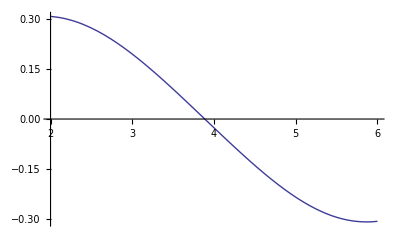

4

54.

```mathematica
ra=1;
rb=1;
ta=0.04;
tb=0.17;
PlotGC[L,√0.001,4,M,ra,ta,rb,tb,2,6]
2(ra^2+rb^2)
optboundaries[L,√0.001,20,M,ra,ta,rb,tb]
```

Test the optimum drb finder

```mathematica
step=0.01;
stop=0.5;
testplot=Table[optboundaries[L,√0.001,4,M,1,a,1,b],{a,step,stop,step},{b,step,stop,step}];
```

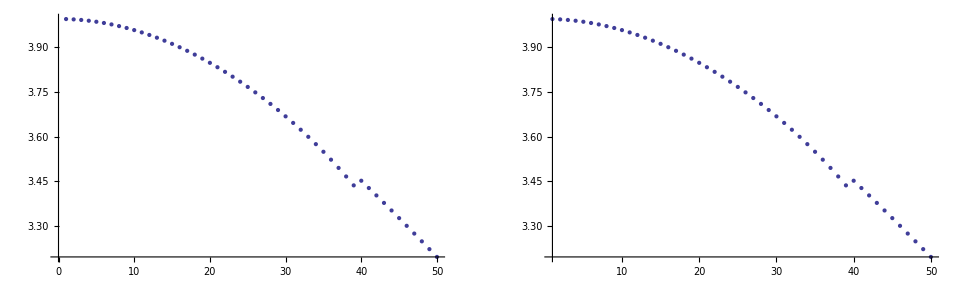

```mathematica
GraphicsRow[{ListPlot[testplot[[4]]],
ListPlot[testplot[[4]],PlotRange->All]}]
```

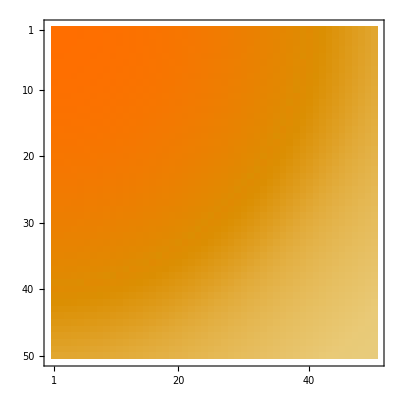

```mathematica
MatrixPlot[testplot]
```

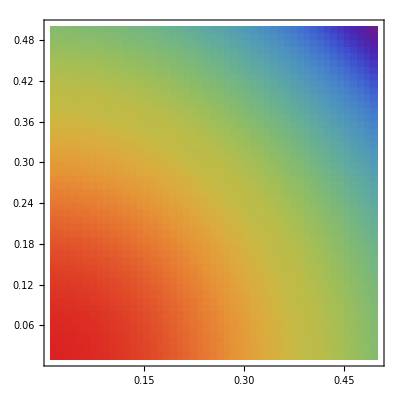

```mathematica
ListDensityPlot[testplot,ColorFunction->"Rainbow",PlotRange->{2,4},DataRange->{{0.01,0.5},{0.01,0.5}}]
```

#### σ_Δ^2 = 0.001, 20 dB

```mathematica
σΔ=√0.001;
SNRdB=20;
```

```mathematica
DistributeDefinitions[σΔ,SNRdB];
```

Define the distributions

```mathematica
Tikhonov[y_,σ_]:=Tikhonov[y,σ]=Exp[Cos[2 Pi y]/(2Pi σ)^2]/BesselI[0,1/(2 Pi σ)^2]
Rayleigh[y_]:=Rayleigh[y]=PDF[NakagamiDistribution[1,2 (Sqrt[2/Pi] )^2],y]
σΔ1=0.01;
σΔ2=0.01;
```

Unproven: Average the conditional BER over the distributions (Gauss-Legendre for Tikhonov, I used a linear sampling for the Rayleigh)

```mathematica
gqtikh1=GaussianQuadratureWeights[10,0,1/2];
gqtikh2=GaussianQuadratureWeights[10,0,1/2];
gqrayl1=GaussianQuadratureWeights[10,0,3];
gqrayl2=GaussianQuadratureWeights[10,0,3];
iΔ1=gqtikh1[[All,1]];
wΔ1=gqtikh1[[All,2]];
sizeΔ1=Length[iΔ1];
iΔ2=gqtikh2[[All,1]];
wΔ2=gqtikh2[[All,2]];
sizeΔ2=Length[iΔ2];
(*ir1=gqrayl1[[All,1]];
wr1=gqrayl1[[All,2]];*)
ir1 = Range[0.03,3,0.03];
wr1=Table[1/Length[ir1],{Length[ir1]}];
sizer1=Length[ir1];
(*ir2=gqrayl2[[All,1]];
wr2=gqrayl2[[All,2]];*)
ir2 = Range[0.03,3,0.03];
wr2=Table[1/Length[ir2],{Length[ir2]}];
sizer2=Length[ir2];
iΔ1grid = Table[iΔ1,{sizeΔ2},{sizer1},{sizer2}];
wΔ1grid = Table[wΔ1,{sizeΔ2},{sizer1},{sizer2}];
iΔ2grid = Table[Table[iΔ2[[c]],{sizeΔ1}],{sizer1},{sizer2},{c,sizeΔ2}];
wΔ2grid = Table[Table[wΔ2[[c]],{sizeΔ1}],{sizer1},{sizer2},{c,sizeΔ2}];
ir1grid = Table[Table[ir1[[c]],{sizeΔ2},{sizeΔ1}],{sizer2},{c,sizer1}];
wr1grid = Table[Table[wr1[[c]],{sizeΔ2},{sizeΔ1}],{sizer2},{c,sizer1}];
ir2grid = Table[Table[ir2[[c]],{sizer1},{sizeΔ2},{sizeΔ1}],{c,sizer2}];
wr2grid = Table[Table[wr2[[c]],{sizer1},{sizeΔ2},{sizeΔ1}],{c,sizer2}];
iΔ1grid[[1,1,1,All]]
iΔ2grid[[1,1,All,1]]
ir1grid[[1,All,1,1]]
ir2grid[[All,1,1,1]]
roots = Table[optboundaries[L,σΔ,SNRdB,M,ir1grid[[a,b,c,d]],iΔ1grid[[a,b,c,d]],ir2grid[[a,b,c,d]],iΔ2grid[[a,b,c,d]]],{a,sizer2},{b,sizer1},{c,sizeΔ2},{d,sizeΔ1}];
MatrixPlot[roots[[All,All,1,1]],PlotLabel->"Roots",PlotLegends->Automatic,DataRange->{{0.1,3},{0.1,3}}]
MatrixPlot[roots[[1,1,All,All]],PlotLabel->"Roots",PlotLegends->Automatic]
unweightedBER=Table[GetBER[L,σΔ,SNRdB,M,ir1grid[[a,b,c,d]],iΔ1grid[[a,b,c,d]],ir2grid[[a,b,c,d]],iΔ2grid[[a,b,c,d]],roots[[a,b,c,d]]],{a,sizer2},{b,sizer1},{c,sizeΔ2},{d,sizeΔ1}];
MatrixPlot[unweightedBER[[All,All,1,1]],PlotLabel->"Roots",PlotLegends->Automatic,DataRange->{{0.1,3},{0.1,3}}]
MatrixPlot[unweightedBER[[1,1,All,All]],PlotLabel->"Roots",PlotLegends->Automatic]
weightedBER = wΔ1grid*Tikhonov[iΔ1grid,σΔ1]*wΔ2grid*Tikhonov[iΔ2grid,σΔ2]* wr1grid*Rayleigh[ir1grid]* wr2grid*Rayleigh[ir2grid]*unweightedBER;
MatrixPlot[weightedBER[[All,All,1,1]],PlotLabel->"Roots",PlotLegends->Automatic,DataRange->{{0.1,3},{0.1,3}}]
MatrixPlot[weightedBER[[1,1,All,All]],PlotLabel->"Roots",PlotLegends->Automatic]
BER = Total[Total[Total[Total[weightedBER]]]]
```

```mathematica
MatrixPlot[weightedBER,PlotLegends->Automatic,PlotLabel->"Gauss-Legendre weighted BER vs Timing Offset, L=2"]
```

```mathematica
allboundaries=ParallelTable[optboundaries[n,L,σΔ,SNRdB,m],{n,1,20},{m,1,M}];
allboundaries // MatrixForm
```

(1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447
1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835 | 1.95835
1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809 | 1.98809
1.97133 | 1.93649 | 1.95342 | 1.95395 | 1.95325 | 1.95246 | 1.95197 | 1.95176 | 1.95174 | 1.95173 | 1.9516 | 1.95138 | 1.95115 | 1.95098 | 1.95088 | 1.95084 | 1.95084 | 1.95084 | 1.95083 | 1.9508
1.95062 | 1.95056 | 1.95061 | 1.95062 | 1.95062 | 1.95064 | 1.95065 | 1.95065 | 1.95065 | 1.95066 | 1.95066 | 1.95066 | 1.95067 | 1.95067 | 1.95067 | 1.95066 | 1.95066 | 1.95067 | 1.95067 | 1.95067
1.97317 | 1.97317 | 1.97316 | 1.97316 | 1.97315 | 1.97315 | 1.97316 | 1.97316 | 1.97315 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316 | 1.97316
1.98101 | 2.00097 | 1.96133 | 1.96137 | 1.96763 | 1.96943 | 1.96862 | 1.96817 | 1.96816 | 1.96806 | 1.96787 | 1.96772 | 1.96765 | 1.96764 | 1.96766 | 1.96768 | 1.96768 | 1.96767 | 1.96766 | 1.96764
1.95838 | 1.94153 | 1.95155 | 1.95178 | 1.95247 | 1.95234 | 1.95241 | 1.95251 | 1.95252 | 1.95254 | 1.95259 | 1.95265 | 1.95269 | 1.95271 | 1.95271 | 1.9527 | 1.9527 | 1.95271 | 1.95271 | 1.95272
1.9658 | 1.96455 | 1.96539 | 1.96542 | 1.96546 | 1.96544 | 1.96541 | 1.96539 | 1.96539 | 1.96539 | 1.96539 | 1.96538 | 1.96537 | 1.96536 | 1.96536 | 1.96536 | 1.96536 | 1.96536 | 1.96536 | 1.96536
1.97371 | 1.95976 | 1.96334 | 1.96392 | 1.96222 | 1.96448 | 1.96581 | 1.96602 | 1.966 | 1.96601 | 1.96599 | 1.96595 | 1.96592 | 1.96593 | 1.96595 | 1.96597 | 1.96597 | 1.96596 | 1.96595 | 1.96595
1.96966 | 1.9302 | 1.95364 | 1.95371 | 1.95627 | 1.9585 | 1.95878 | 1.95865 | 1.95862 | 1.95863 | 1.95868 | 1.95877 | 1.95884 | 1.95888 | 1.95889 | 1.95888 | 1.95888 | 1.95889 | 1.9589 | 1.95891
1.96627 | 1.95396 | 1.96156 | 1.9616 | 1.9628 | 1.96302 | 1.96278 | 1.96268 | 1.96268 | 1.96269 | 1.96269 | 1.96266 | 1.96263 | 1.96261 | 1.9626 | 1.9626 | 1.9626 | 1.9626 | 1.9626 | 1.96259
1.96939 | 1.96116 | 1.96343 | 1.96383 | 1.96279 | 1.96233 | 1.96296 | 1.96335 | 1.96339 | 1.96336 | 1.96338 | 1.96342 | 1.96347 | 1.9635 | 1.96352 | 1.96354 | 1.96354 | 1.96354 | 1.96353 | 1.96353
1.97006 | 1.9499 | 1.9574 | 1.95786 | 1.95726 | 1.95962 | 1.96103 | 1.96124 | 1.96121 | 1.96128 | 1.96139 | 1.96148 | 1.96153 | 1.96155 | 1.96155 | 1.96155 | 1.96154 | 1.96155 | 1.96156 | 1.96157
1.96864 | 1.94891 | 1.95927 | 1.95931 | 1.96076 | 1.96242 | 1.9626 | 1.96238 | 1.96234 | 1.96237 | 1.96237 | 1.96234 | 1.9623 | 1.96228 | 1.96227 | 1.96227 | 1.96227 | 1.96227 | 1.96227 | 1.96226
1.96871 | 1.95476 | 1.96166 | 1.96185 | 1.96253 | 1.96249 | 1.96235 | 1.96246 | 1.96249 | 1.96243 | 1.9624 | 1.96243 | 1.96248 | 1.96253 | 1.96255 | 1.96256 | 1.96256 | 1.96256 | 1.96257 | 1.96257
1.96921 | 1.95436 | 1.96005 | 1.9605 | 1.95982 | 1.96036 | 1.96137 | 1.96177 | 1.96179 | 1.96183 | 1.96196 | 1.96208 | 1.96215 | 1.96217 | 1.96217 | 1.96217 | 1.96217 | 1.96217 | 1.96218 | 1.96218
1.96909 | 1.95196 | 1.95936 | 1.95963 | 1.95976 | 1.96143 | 1.96228 | 1.9623 | 1.96226 | 1.96232 | 1.96237 | 1.96237 | 1.96234 | 1.96231 | 1.9623 | 1.96231 | 1.96231 | 1.96231 | 1.9623 | 1.9623
1.96895 | 1.95256 | 1.96029 | 1.96046 | 1.96121 | 1.96226 | 1.96241 | 1.96233 | 1.96232 | 1.96229 | 1.96225 | 1.96224 | 1.96227 | 1.9623 | 1.96233 | 1.96233 | 1.96233 | 1.96233 | 1.96233 | 1.96234
1.96901 | 1.95335 | 1.96036 | 1.96065 | 1.9609 | 1.96138 | 1.96176 | 1.96197 | 1.962 | 1.962 | 1.96207 | 1.96217 | 1.96224 | 1.96227 | 1.96227 | 1.96227 | 1.96227 | 1.96228 | 1.96229 | 1.96229)

```mathematica
100*Abs[(allboundaries[[-1,-1]]-allboundaries)/allboundaries[[-1,-1]]] // MatrixForm
```

(9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135 | 9.57135
0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582 | 0.200582
1.31498 | 1.31499 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498 | 1.31498
0.460666 | 1.31485 | 0.452053 | 0.424838 | 0.460515 | 0.500796 | 0.525746 | 0.536624 | 0.537521 | 0.538374 | 0.544781 | 0.555848 | 0.567551 | 0.576481 | 0.581463 | 0.583258 | 0.58347 | 0.583541 | 0.584237 | 0.585623
0.594609 | 0.597882 | 0.59496 | 0.594683 | 0.594636 | 0.593882 | 0.593157 | 0.592925 | 0.592927 | 0.592849 | 0.592664 | 0.592485 | 0.592393 | 0.592382 | 0.592402 | 0.592415 | 0.592412 | 0.5924 | 0.592389 | 0.592385
0.554634 | 0.55423 | 0.553824 | 0.553741 | 0.553531 | 0.553634 | 0.55372 | 0.553707 | 0.553693 | 0.553721 | 0.553764 | 0.553793 | 0.553799 | 0.55379 | 0.553776 | 0.553764 | 0.55376 | 0.553762 | 0.553769 | 0.553779
0.953941 | 1.97098 | 0.0487009 | 0.0468597 | 0.272341 | 0.36375 | 0.322614 | 0.29989 | 0.299292 | 0.294193 | 0.284432 | 0.276747 | 0.273231 | 0.272793 | 0.273715 | 0.274645 | 0.274894 | 0.274433 | 0.273619 | 0.272861
0.199084 | 1.05785 | 0.54734 | 0.535717 | 0.500444 | 0.506958 | 0.503418 | 0.498206 | 0.497713 | 0.497026 | 0.494353 | 0.491185 | 0.489071 | 0.488322 | 0.488361 | 0.488522 | 0.488486 | 0.48827 | 0.488022 | 0.487858
0.178899 | 0.115013 | 0.158057 | 0.159628 | 0.161437 | 0.16045 | 0.159214 | 0.158214 | 0.158058 | 0.158169 | 0.158002 | 0.157555 | 0.157064 | 0.156697 | 0.156489 | 0.156404 | 0.156383 | 0.15638 | 0.156365 | 0.156333
0.581821 | 0.12891 | 0.0536111 | 0.0832083 | 0.00343321 | 0.111506 | 0.179141 | 0.189943 | 0.188848 | 0.18949 | 0.188806 | 0.186446 | 0.184943 | 0.185297 | 0.186516 | 0.187372 | 0.18746 | 0.187071 | 0.18665 | 0.186457
0.375832 | 1.63523 | 0.440911 | 0.43711 | 0.307002 | 0.192995 | 0.17882 | 0.1857 | 0.187012 | 0.186293 | 0.183797 | 0.179482 | 0.175581 | 0.173685 | 0.173436 | 0.173674 | 0.173645 | 0.173253 | 0.172743 | 0.172356
0.202808 | 0.424482 | 0.0373032 | 0.035301 | 0.0260875 | 0.0370171 | 0.0248798 | 0.0200474 | 0.0196808 | 0.0202094 | 0.0201751 | 0.0190726 | 0.0175482 | 0.0164267 | 0.0159517 | 0.0158872 | 0.0159087 | 0.0158379 | 0.0156624 | 0.0154501
0.361935 | 0.0578036 | 0.0583583 | 0.0787348 | 0.0254842 | 0.00182458 | 0.0339846 | 0.0539018 | 0.0560425 | 0.0545192 | 0.0553814 | 0.0577091 | 0.0599654 | 0.0616905 | 0.0628565 | 0.0634701 | 0.0636219 | 0.0635282 | 0.0634271 | 0.0634539
0.395927 | 0.631396 | 0.249289 | 0.225566 | 0.256441 | 0.135926 | 0.0642026 | 0.0534733 | 0.0552452 | 0.0515829 | 0.0457803 | 0.0413649 | 0.0388474 | 0.0378232 | 0.0377312 | 0.0379362 | 0.0379641 | 0.0376907 | 0.0372693 | 0.0369134
0.32383 | 0.682048 | 0.153759 | 0.151829 | 0.0777123 | 0.00671159 | 0.0157921 | 0.00468044 | 0.00247594 | 0.0039062 | 0.00386536 | 0.00238883 | 0.000693522 | 0.000476687 | 0.000960019 | 0.00098793 | 0.000914947 | 0.000973996 | 0.00119349 | 0.00147249
0.327389 | 0.383972 | 0.0322093 | 0.022562 | 0.0121819 | 0.0103242 | 0.00324489 | 0.00847794 | 0.0102084 | 0.00734645 | 0.00577977 | 0.00718084 | 0.00984712 | 0.0121243 | 0.0134333 | 0.0139264 | 0.0139983 | 0.0139871 | 0.0140654 | 0.0142535
0.352438 | 0.404076 | 0.114098 | 0.0910053 | 0.125994 | 0.0983199 | 0.0469042 | 0.0264486 | 0.025481 | 0.0233137 | 0.0167326 | 0.0104592 | 0.00706226 | 0.00608828 | 0.00616949 | 0.00634436 | 0.00627215 | 0.00599341 | 0.00567382 | 0.00544849
0.346676 | 0.526651 | 0.149125 | 0.135414 | 0.128825 | 0.0438631 | 0.000746175 | 0.000512848 | 0.00172345 | 0.00146761 | 0.0041502 | 0.00391675 | 0.0023686 | 0.00118238 | 0.000760252 | 0.000776936 | 0.000846078 | 0.000780949 | 0.000586161 | 0.00035683
0.339616 | 0.496014 | 0.101911 | 0.0933887 | 0.0549617 | 0.00149942 | 0.00606064 | 0.00226603 | 0.00169427 | 0.0002578 | 0.00191058 | 0.00236751 | 0.00101967 | 0.000716172 | 0.00183862 | 0.00222862 | 0.00222795 | 0.00218562 | 0.0022652 | 0.00245978
0.342505 | 0.455535 | 0.0983079 | 0.0836775 | 0.0707123 | 0.0464685 | 0.0270633 | 0.0160746 | 0.0147304 | 0.0148949 | 0.0114316 | 0.00625312 | 0.00250272 | 0.000989767 | 0.00080959 | 0.000908798 | 0.000806693 | 0.000511211 | 0.000199065 | 0.)

#### σ_Δ^2 = 0.005, 20 dB

```mathematica
σΔ=√0.005;
SNRdB=20;
```

```mathematica
DistributeDefinitions[σΔ,SNRdB];
```

```mathematica
gq=GaussianQuadratureWeights[10,0,1/2];
Δi=gq[[All,1]];
wi=gq[[All,2]];
GCparams=GC[L,σΔ,SNRdB,M,Δi];
g0=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
```

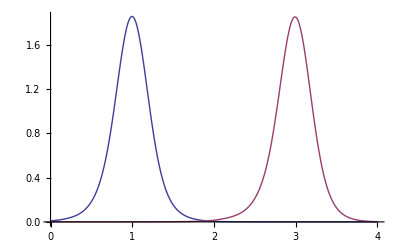

```mathematica
Plot[{2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) σX[[i]]) Exp[-(y - g0[[i]])^2/(2 σX[[i]]^2)] (1 + ∑_(m=2)^M α[[i,m]]/((2 m)! σX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - g0[[i]])/(√2 σX[[i]])]),2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) σX[[i]]) Exp[-(y - 3 g0[[i]])^2/(2 σX[[i]]^2)] (1 + ∑_(m=2)^M α[[i,m]]/((2 m)! σX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - 3 g0[[i]])/(√2 σX[[i]])])},{y,0,4},PlotRange->All]
```

```mathematica
optboundaries[10,L,σΔ,SNRdB,M]
```

1.90853

```mathematica
allboundaries=ParallelTable[optboundaries[n,L,σΔ,SNRdB,m],{n,1,20},{m,1,M}];
allboundaries // MatrixForm
```

(1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447
1.95807 | 1.95815 | 1.95826 | 1.95837 | 1.95841 | 1.95841 | 1.95839 | 1.95837 | 1.95835 | 1.95834 | 1.95834 | 1.95834 | 1.95834 | 1.95834 | 1.95834 | 1.95834 | 1.95833 | 1.95833 | 1.95833 | 1.95833
1.83463 | 1.80684 | 1.81223 | 1.81072 | 1.81104 | 1.81215 | 1.81304 | 1.8136 | 1.8138 | 1.81377 | 1.81375 | 1.81391 | 1.81427 | 1.81476 | 1.81525 | 1.81562 | 1.81578 | 1.81573 | 1.81551 | 1.81521
1.89852 | 1.89893 | 1.89916 | 1.89924 | 1.89926 | 1.89927 | 1.89928 | 1.8993 | 1.89932 | 1.89934 | 1.89935 | 1.89935 | 1.89935 | 1.89934 | 1.89932 | 1.89931 | 1.89931 | 1.8993 | 1.89931 | 1.89931
1.93654 | 1.9367 | 1.9329 | 1.93148 | 1.93114 | 1.93047 | 1.9301 | 1.93026 | 1.93044 | 1.93033 | 1.93006 | 1.92991 | 1.93001 | 1.93029 | 1.93061 | 1.93083 | 1.93092 | 1.93087 | 1.93073 | 1.93055
1.89869 | 1.8808 | 1.87794 | 1.87791 | 1.87668 | 1.87679 | 1.87734 | 1.87752 | 1.87757 | 1.87769 | 1.87785 | 1.87793 | 1.87792 | 1.87784 | 1.87775 | 1.87769 | 1.87766 | 1.87767 | 1.8777 | 1.87773
1.91084 | 1.91027 | 1.91064 | 1.91001 | 1.91021 | 1.91075 | 1.91114 | 1.91131 | 1.91138 | 1.91143 | 1.91151 | 1.91162 | 1.91175 | 1.91187 | 1.91197 | 1.91203 | 1.91206 | 1.91206 | 1.91202 | 1.91195
1.91849 | 1.91648 | 1.91014 | 1.9085 | 1.9087 | 1.9078 | 1.9065 | 1.90583 | 1.90577 | 1.90589 | 1.90599 | 1.90607 | 1.90615 | 1.90622 | 1.90625 | 1.90623 | 1.90619 | 1.90619 | 1.90623 | 1.90633
1.91164 | 1.90337 | 1.89913 | 1.89881 | 1.89751 | 1.89676 | 1.89705 | 1.89747 | 1.8976 | 1.89757 | 1.89757 | 1.89763 | 1.89773 | 1.89783 | 1.89791 | 1.89797 | 1.898 | 1.89799 | 1.89795 | 1.89789
1.91255 | 1.90853 | 1.90682 | 1.90567 | 1.9059 | 1.90679 | 1.90715 | 1.90706 | 1.90702 | 1.90724 | 1.90762 | 1.90799 | 1.90825 | 1.90839 | 1.90844 | 1.90844 | 1.90844 | 1.90845 | 1.90848 | 1.90853
1.91398 | 1.91051 | 1.9062 | 1.90507 | 1.9053 | 1.90465 | 1.90366 | 1.90319 | 1.9032 | 1.90326 | 1.90316 | 1.90297 | 1.90278 | 1.90268 | 1.90264 | 1.90264 | 1.90264 | 1.90262 | 1.90259 | 1.90255
1.91331 | 1.90821 | 1.90412 | 1.90336 | 1.90265 | 1.90202 | 1.90202 | 1.90223 | 1.9023 | 1.90231 | 1.90243 | 1.90269 | 1.90298 | 1.90322 | 1.90336 | 1.90341 | 1.90342 | 1.90342 | 1.90343 | 1.90345
1.91318 | 1.90845 | 1.90525 | 1.90422 | 1.90408 | 1.90439 | 1.90452 | 1.90441 | 1.9044 | 1.90462 | 1.90491 | 1.90511 | 1.90517 | 1.90512 | 1.90506 | 1.90502 | 1.90501 | 1.90502 | 1.90504 | 1.90504
1.91335 | 1.909 | 1.9054 | 1.90438 | 1.90442 | 1.90417 | 1.90367 | 1.9034 | 1.90341 | 1.90346 | 1.90343 | 1.90337 | 1.90334 | 1.90338 | 1.90344 | 1.90348 | 1.9035 | 1.90348 | 1.90345 | 1.90342
1.91335 | 1.9088 | 1.90504 | 1.90412 | 1.90382 | 1.90341 | 1.9032 | 1.9032 | 1.90324 | 1.9033 | 1.90345 | 1.90367 | 1.90389 | 1.90403 | 1.90409 | 1.9041 | 1.90409 | 1.9041 | 1.90412 | 1.90414
1.91331 | 1.90871 | 1.90511 | 1.90414 | 1.9039 | 1.90381 | 1.90375 | 1.90367 | 1.90368 | 1.90383 | 1.90403 | 1.90416 | 1.9042 | 1.90419 | 1.90417 | 1.90416 | 1.90417 | 1.90417 | 1.90417 | 1.90415
1.91332 | 1.90877 | 1.90518 | 1.9042 | 1.90407 | 1.90392 | 1.90366 | 1.9035 | 1.90351 | 1.9036 | 1.90367 | 1.90372 | 1.90377 | 1.90383 | 1.90388 | 1.90392 | 1.90392 | 1.90391 | 1.9039 | 1.90389
1.91332 | 1.90878 | 1.90515 | 1.90418 | 1.904 | 1.90375 | 1.90351 | 1.90342 | 1.90344 | 1.90353 | 1.90366 | 1.90381 | 1.90394 | 1.90402 | 1.90406 | 1.90406 | 1.90406 | 1.90406 | 1.90407 | 1.90408
1.91332 | 1.90877 | 1.90514 | 1.90417 | 1.90396 | 1.90377 | 1.9036 | 1.90351 | 1.90353 | 1.90364 | 1.90379 | 1.90392 | 1.90399 | 1.90402 | 1.90404 | 1.90404 | 1.90405 | 1.90405 | 1.90405 | 1.90404
1.91332 | 1.90877 | 1.90515 | 1.90418 | 1.90399 | 1.90382 | 1.90362 | 1.9035 | 1.90352 | 1.90362 | 1.90373 | 1.90383 | 1.9039 | 1.90395 | 1.90399 | 1.90401 | 1.90401 | 1.90401 | 1.904 | 1.904)

```mathematica
100*Abs[(allboundaries[[-1,-1]]-allboundaries)/allboundaries[[-1,-1]]] // MatrixForm
```

(6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293 | 6.80293
2.8399 | 2.84378 | 2.84977 | 2.85549 | 2.85772 | 2.85786 | 2.85671 | 2.85541 | 2.85458 | 2.85422 | 2.85414 | 2.85419 | 2.85422 | 2.85417 | 2.85404 | 2.85387 | 2.85369 | 2.85354 | 2.85345 | 2.8534
3.6432 | 5.10319 | 4.8199 | 4.89913 | 4.88235 | 4.82429 | 4.77729 | 4.74764 | 4.73742 | 4.73901 | 4.73987 | 4.73152 | 4.7125 | 4.68678 | 4.66108 | 4.64194 | 4.63341 | 4.63606 | 4.64745 | 4.66357
0.287589 | 0.266386 | 0.253968 | 0.249795 | 0.248807 | 0.248431 | 0.247729 | 0.246685 | 0.245545 | 0.244607 | 0.244092 | 0.244061 | 0.244424 | 0.245008 | 0.245637 | 0.246164 | 0.246499 | 0.246613 | 0.246528 | 0.246307
1.70917 | 1.71766 | 1.51812 | 1.44341 | 1.42524 | 1.39034 | 1.37081 | 1.37908 | 1.38852 | 1.38263 | 1.36861 | 1.36076 | 1.36594 | 1.38079 | 1.3974 | 1.40935 | 1.41389 | 1.41144 | 1.40412 | 1.39441
0.278806 | 1.21852 | 1.3689 | 1.3703 | 1.43499 | 1.42906 | 1.4002 | 1.39064 | 1.38839 | 1.38183 | 1.3735 | 1.36899 | 1.36983 | 1.374 | 1.3787 | 1.38208 | 1.38346 | 1.38303 | 1.3815 | 1.37972
0.359259 | 0.329555 | 0.348522 | 0.315542 | 0.325942 | 0.354767 | 0.374856 | 0.38418 | 0.387656 | 0.390237 | 0.394407 | 0.400231 | 0.40678 | 0.413086 | 0.418357 | 0.421979 | 0.423579 | 0.423134 | 0.420989 | 0.417768
0.761189 | 0.655539 | 0.322652 | 0.236522 | 0.247069 | 0.199803 | 0.131501 | 0.096093 | 0.092751 | 0.0992513 | 0.104588 | 0.108699 | 0.113041 | 0.116693 | 0.117999 | 0.116891 | 0.115104 | 0.114825 | 0.117314 | 0.122404
0.40129 | 0.0328531 | 0.25562 | 0.272335 | 0.340698 | 0.380355 | 0.365044 | 0.342978 | 0.336307 | 0.337849 | 0.337954 | 0.334462 | 0.329271 | 0.324124 | 0.319787 | 0.316692 | 0.31526 | 0.315716 | 0.317868 | 0.321118
0.448804 | 0.23803 | 0.148133 | 0.0874656 | 0.0995744 | 0.146605 | 0.165524 | 0.160496 | 0.158536 | 0.170343 | 0.190226 | 0.209425 | 0.223048 | 0.230345 | 0.23295 | 0.233194 | 0.233029 | 0.233603 | 0.235307 | 0.238011
0.524344 | 0.341721 | 0.115507 | 0.0564472 | 0.0680359 | 0.0338823 | 0.0180486 | 0.0422988 | 0.0419365 | 0.0389266 | 0.0438641 | 0.0542629 | 0.0639242 | 0.0695127 | 0.0713755 | 0.0714567 | 0.0714596 | 0.0722343 | 0.0739403 | 0.0763887
0.489104 | 0.221177 | 0.00617911 | 0.0333577 | 0.0708475 | 0.103965 | 0.104134 | 0.0931871 | 0.0894387 | 0.0888049 | 0.0822971 | 0.068807 | 0.0534027 | 0.0410971 | 0.0338174 | 0.0308103 | 0.0302085 | 0.0302754 | 0.0299465 | 0.0288523
0.482183 | 0.233776 | 0.0654282 | 0.0113166 | 0.00397399 | 0.0206956 | 0.0273412 | 0.0214525 | 0.0209752 | 0.032466 | 0.0480016 | 0.0584991 | 0.061309 | 0.0590665 | 0.0556616 | 0.0535242 | 0.0531199 | 0.053733 | 0.0544098 | 0.0545153
0.491265 | 0.262738 | 0.0734236 | 0.0198635 | 0.0218529 | 0.00897798 | 0.0173459 | 0.031492 | 0.0311118 | 0.0284039 | 0.0298339 | 0.0332131 | 0.0345547 | 0.0328002 | 0.029615 | 0.0271391 | 0.026443 | 0.0273305 | 0.0289225 | 0.0303247
0.490838 | 0.252085 | 0.0546285 | 0.00627914 | 0.00956093 | 0.0310938 | 0.0421335 | 0.0422561 | 0.0400914 | 0.0365099 | 0.028624 | 0.0171293 | 0.00600107 | 0.00144559 | 0.00463663 | 0.00510845 | 0.00484667 | 0.00509846 | 0.00611373 | 0.00749855
0.489138 | 0.247288 | 0.0581562 | 0.0073232 | 0.00531169 | 0.00983034 | 0.0132898 | 0.0173257 | 0.0165516 | 0.00878466 | 0.00132915 | 0.00827073 | 0.0104689 | 0.00980404 | 0.00874807 | 0.00847959 | 0.00880989 | 0.0090316 | 0.00867007 | 0.00773383
0.48946 | 0.25072 | 0.0619884 | 0.0103712 | 0.00351307 | 0.00422698 | 0.0176983 | 0.026162 | 0.0256402 | 0.0211309 | 0.0173737 | 0.0148319 | 0.0121553 | 0.00896304 | 0.00609059 | 0.00444159 | 0.00417035 | 0.00472366 | 0.00535259 | 0.00557168
0.489738 | 0.251282 | 0.0602638 | 0.00967596 | 0.0000781954 | 0.013192 | 0.0257437 | 0.0305459 | 0.0292171 | 0.0246566 | 0.0178888 | 0.0100743 | 0.00321932 | 0.00114415 | 0.00293912 | 0.00319759 | 0.0030886 | 0.00324312 | 0.00368431 | 0.00412838
0.489653 | 0.25044 | 0.0596836 | 0.00904086 | 0.0019155 | 0.0122231 | 0.02126 | 0.0257334 | 0.0246294 | 0.0186926 | 0.0108237 | 0.00427029 | 0.000449876 | 0.00119574 | 0.00187935 | 0.00235152 | 0.00270565 | 0.00276276 | 0.00245392 | 0.00192343
0.48961 | 0.25041 | 0.0601812 | 0.00925926 | 0.000490921 | 0.00970768 | 0.0201818 | 0.0261864 | 0.0253568 | 0.0201165 | 0.0140937 | 0.00912258 | 0.00531897 | 0.00242359 | 0.000446549 | 0.000531897 | 0.000674369 | 0.000386 | 0.0000849325 | 0.)

#### σ_Δ^2 = 0.01, 20 dB

```mathematica
σΔ=√0.01;
SNRdB=20;
```

```mathematica
DistributeDefinitions[σΔ,SNRdB];
```

```mathematica
gq=GaussianQuadratureWeights[10,0,1/2];
Δi=gq[[All,1]];
wi=gq[[All,2]];
GCparams=GC[L,σΔ,SNRdB,M,Δi];
g0=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
```

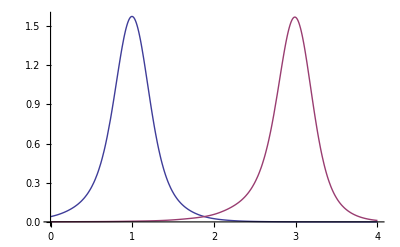

```mathematica
Plot[{2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) σX[[i]]) Exp[-(y - g0[[i]])^2/(2 σX[[i]]^2)] (1 + ∑_(m=2)^M α[[i,m]]/((2 m)! σX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - g0[[i]])/(√2 σX[[i]])]),2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) σX[[i]]) Exp[-(y - 3 g0[[i]])^2/(2 σX[[i]]^2)] (1 + ∑_(m=2)^M α[[i,m]]/((2 m)! σX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - 3 g0[[i]])/(√2 σX[[i]])])},{y,0,4},PlotRange->All]
```

```mathematica
optboundaries[10,L,σΔ,SNRdB,M]
```

1.88167

```mathematica
allboundaries=ParallelTable[optboundaries[n,L,σΔ,SNRdB,m],{n,1,20},{m,1,M}];
allboundaries // MatrixForm
```

(1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447 | 1.77447
1.94353 | 1.94737 | 1.95337 | 1.95913 | 1.96139 | 1.96153 | 1.96036 | 1.95906 | 1.95822 | 1.95785 | 1.95778 | 1.95782 | 1.95785 | 1.95781 | 1.95768 | 1.9575 | 1.95732 | 1.95716 | 1.95706 | 1.95702
1.78271 | 1.77833 | 1.78178 | 1.78304 | 1.78371 | 1.78401 | 1.78388 | 1.78343 | 1.78286 | 1.78235 | 1.78203 | 1.78191 | 1.78196 | 1.78212 | 1.78229 | 1.78243 | 1.78248 | 1.78245 | 1.78234 | 1.7822
1.88555 | 1.89167 | 1.89502 | 1.89634 | 1.8967 | 1.89679 | 1.89688 | 1.89704 | 1.89722 | 1.89738 | 1.89746 | 1.89744 | 1.89734 | 1.8972 | 1.89705 | 1.89692 | 1.89684 | 1.89682 | 1.89685 | 1.89691
1.88076 | 1.88438 | 1.87728 | 1.87555 | 1.87556 | 1.87465 | 1.87401 | 1.87411 | 1.87422 | 1.87389 | 1.87342 | 1.87327 | 1.87361 | 1.87431 | 1.87504 | 1.87555 | 1.87571 | 1.87554 | 1.87514 | 1.87464
1.86034 | 1.85936 | 1.86264 | 1.86423 | 1.8641 | 1.86422 | 1.86468 | 1.86511 | 1.8654 | 1.86553 | 1.86549 | 1.86528 | 1.865 | 1.86472 | 1.8645 | 1.86437 | 1.8643 | 1.86428 | 1.86427 | 1.86426
1.87594 | 1.8844 | 1.88636 | 1.88576 | 1.88657 | 1.88813 | 1.88923 | 1.88969 | 1.88982 | 1.88996 | 1.89023 | 1.8906 | 1.89098 | 1.89134 | 1.89161 | 1.89177 | 1.89183 | 1.89177 | 1.89162 | 1.89143
1.87324 | 1.87695 | 1.87415 | 1.87414 | 1.8747 | 1.87405 | 1.87317 | 1.87289 | 1.87305 | 1.87321 | 1.87318 | 1.873 | 1.87278 | 1.87258 | 1.87241 | 1.87229 | 1.87221 | 1.87217 | 1.87216 | 1.87217
1.87093 | 1.87369 | 1.87473 | 1.87517 | 1.87489 | 1.87534 | 1.87636 | 1.87711 | 1.87734 | 1.87733 | 1.87738 | 1.87759 | 1.8779 | 1.87823 | 1.87849 | 1.87863 | 1.87866 | 1.8786 | 1.87848 | 1.87834
1.87237 | 1.87751 | 1.87817 | 1.87782 | 1.87873 | 1.87995 | 1.88045 | 1.88046 | 1.88056 | 1.88091 | 1.88136 | 1.88172 | 1.88188 | 1.88189 | 1.88181 | 1.88173 | 1.88168 | 1.88166 | 1.88167 | 1.88167
1.87238 | 1.87682 | 1.87631 | 1.87638 | 1.87686 | 1.8768 | 1.87664 | 1.87675 | 1.87694 | 1.87696 | 1.87681 | 1.87664 | 1.87656 | 1.87661 | 1.87671 | 1.87678 | 1.87679 | 1.87672 | 1.87659 | 1.87644
1.87211 | 1.87611 | 1.87624 | 1.87632 | 1.87646 | 1.87693 | 1.87759 | 1.87803 | 1.87821 | 1.87836 | 1.87865 | 1.87904 | 1.87942 | 1.87968 | 1.8798 | 1.87982 | 1.87979 | 1.87976 | 1.87974 | 1.87973
1.87217 | 1.87649 | 1.87673 | 1.87666 | 1.87721 | 1.87795 | 1.87836 | 1.87849 | 1.87864 | 1.87886 | 1.87907 | 1.87916 | 1.87914 | 1.87909 | 1.87905 | 1.87903 | 1.87901 | 1.87897 | 1.87889 | 1.87878
1.8722 | 1.87656 | 1.87658 | 1.87658 | 1.87706 | 1.87743 | 1.87762 | 1.8778 | 1.87797 | 1.87806 | 1.87811 | 1.87818 | 1.87831 | 1.87848 | 1.87861 | 1.87867 | 1.87866 | 1.8786 | 1.87853 | 1.87846
1.87219 | 1.87646 | 1.87651 | 1.87653 | 1.87688 | 1.87733 | 1.87774 | 1.87803 | 1.87821 | 1.87837 | 1.87858 | 1.87883 | 1.87903 | 1.87915 | 1.87919 | 1.87919 | 1.87916 | 1.87912 | 1.87908 | 1.87902
1.87218 | 1.87646 | 1.87656 | 1.87655 | 1.87698 | 1.87753 | 1.87792 | 1.87813 | 1.87829 | 1.87846 | 1.87863 | 1.87874 | 1.87881 | 1.87886 | 1.8789 | 1.87892 | 1.87891 | 1.87887 | 1.87879 | 1.8787
1.87219 | 1.87648 | 1.87656 | 1.87656 | 1.87701 | 1.87749 | 1.87781 | 1.87802 | 1.87818 | 1.87831 | 1.87844 | 1.87857 | 1.87871 | 1.87884 | 1.87892 | 1.87895 | 1.87893 | 1.87888 | 1.87882 | 1.87875
1.87219 | 1.87648 | 1.87655 | 1.87655 | 1.87697 | 1.87744 | 1.8778 | 1.87804 | 1.8782 | 1.87836 | 1.87853 | 1.8787 | 1.87885 | 1.87895 | 1.879 | 1.87901 | 1.87899 | 1.87895 | 1.87889 | 1.87882
1.87219 | 1.87648 | 1.87655 | 1.87655 | 1.87697 | 1.87747 | 1.87783 | 1.87806 | 1.87823 | 1.87838 | 1.87854 | 1.87869 | 1.8788 | 1.87889 | 1.87894 | 1.87896 | 1.87895 | 1.87891 | 1.87884 | 1.87876
1.87219 | 1.87648 | 1.87656 | 1.87655 | 1.87698 | 1.87747 | 1.87782 | 1.87805 | 1.87821 | 1.87836 | 1.87851 | 1.87865 | 1.87878 | 1.87889 | 1.87895 | 1.87897 | 1.87896 | 1.87891 | 1.87885 | 1.87878)

```mathematica
100*Abs[(allboundaries[[-1,-1]]-allboundaries)/allboundaries[[-1,-1]]] // MatrixForm
```

(5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168 | 5.55168
3.44636 | 3.65114 | 3.97015 | 4.27706 | 4.39712 | 4.40448 | 4.34252 | 4.27298 | 4.22847 | 4.20872 | 4.20488 | 4.20742 | 4.20908 | 4.20647 | 4.19955 | 4.19008 | 4.18034 | 4.17225 | 4.16686 | 4.1644
5.11333 | 5.34659 | 5.16287 | 5.09591 | 5.05997 | 5.04385 | 5.05091 | 5.0749 | 5.10543 | 5.13233 | 5.14954 | 5.15575 | 5.15298 | 5.14483 | 5.13538 | 5.12817 | 5.12534 | 5.12728 | 5.13291 | 5.14039
0.360399 | 0.686461 | 0.864792 | 0.934651 | 0.954249 | 0.958678 | 0.963598 | 0.971955 | 0.981883 | 0.990242 | 0.994402 | 0.993432 | 0.988176 | 0.980498 | 0.972472 | 0.965847 | 0.961748 | 0.960547 | 0.961933 | 0.965092
0.105838 | 0.29836 | 0.0798086 | 0.171554 | 0.171129 | 0.219826 | 0.25384 | 0.248397 | 0.2427 | 0.260047 | 0.285119 | 0.293204 | 0.274715 | 0.237863 | 0.198899 | 0.171821 | 0.163215 | 0.172263 | 0.193501 | 0.22029
0.981094 | 1.0335 | 0.858747 | 0.774418 | 0.781305 | 0.774687 | 0.750357 | 0.727599 | 0.712043 | 0.704949 | 0.70738 | 0.718079 | 0.733105 | 0.747958 | 0.759598 | 0.766996 | 0.770632 | 0.771774 | 0.771927 | 0.77244
0.151164 | 0.29914 | 0.403847 | 0.371585 | 0.41499 | 0.497962 | 0.556621 | 0.580855 | 0.587953 | 0.595355 | 0.609659 | 0.629147 | 0.649827 | 0.668476 | 0.682958 | 0.691886 | 0.694609 | 0.691432 | 0.683684 | 0.673474
0.294462 | 0.0971106 | 0.246437 | 0.246752 | 0.216994 | 0.251497 | 0.298509 | 0.313206 | 0.304607 | 0.296247 | 0.298053 | 0.30756 | 0.319299 | 0.329981 | 0.338658 | 0.345185 | 0.349426 | 0.351445 | 0.351871 | 0.351796
0.417501 | 0.27081 | 0.215168 | 0.192092 | 0.207036 | 0.182701 | 0.128395 | 0.0888886 | 0.0764069 | 0.0767476 | 0.074227 | 0.0632208 | 0.04638 | 0.0289878 | 0.0153363 | 0.00761894 | 0.0060613 | 0.00946747 | 0.0159026 | 0.0234056
0.341174 | 0.0673493 | 0.0324925 | 0.0509089 | 0.0022582 | 0.0625212 | 0.0890016 | 0.0897928 | 0.0948625 | 0.113686 | 0.1378 | 0.15651 | 0.165238 | 0.165494 | 0.161519 | 0.157172 | 0.154455 | 0.153593 | 0.153818 | 0.154197
0.340248 | 0.103929 | 0.131157 | 0.127315 | 0.102024 | 0.105065 | 0.113476 | 0.107746 | 0.097754 | 0.0966078 | 0.10464 | 0.113864 | 0.11768 | 0.115278 | 0.110035 | 0.106006 | 0.10565 | 0.109377 | 0.116144 | 0.124369
0.354841 | 0.141715 | 0.135194 | 0.130747 | 0.123019 | 0.098207 | 0.0633465 | 0.0396436 | 0.0299309 | 0.0219912 | 0.00688725 | 0.0140078 | 0.034026 | 0.0479092 | 0.0544466 | 0.0555387 | 0.054075 | 0.0523056 | 0.0512405 | 0.0507742
0.351771 | 0.121628 | 0.109069 | 0.112764 | 0.083524 | 0.0437869 | 0.0221853 | 0.0150596 | 0.00736034 | 0.0047161 | 0.0155207 | 0.0203214 | 0.0195572 | 0.0166261 | 0.0143322 | 0.013285 | 0.0124232 | 0.0103343 | 0.00623797 | 0.000273874
0.349798 | 0.118188 | 0.116955 | 0.116737 | 0.0911769 | 0.0717411 | 0.0614349 | 0.0516745 | 0.0428406 | 0.0380195 | 0.0356442 | 0.0317232 | 0.0245905 | 0.0160115 | 0.0090597 | 0.00576866 | 0.00627269 | 0.00932103 | 0.0133018 | 0.0169701
0.350638 | 0.123372 | 0.120677 | 0.119699 | 0.10066 | 0.077222 | 0.0551655 | 0.0396641 | 0.0303786 | 0.0217653 | 0.0102387 | 0.0027627 | 0.0135895 | 0.019989 | 0.0221844 | 0.0217948 | 0.0203445 | 0.0185134 | 0.0162376 | 0.0131726
0.35085 | 0.123117 | 0.117917 | 0.11836 | 0.0955296 | 0.0662927 | 0.0455225 | 0.0341814 | 0.0256952 | 0.0165773 | 0.00802559 | 0.00182402 | 0.00205527 | 0.00469833 | 0.00673295 | 0.00785846 | 0.00739405 | 0.00499587 | 0.000955074 | 0.00394282
0.350689 | 0.122084 | 0.11773 | 0.117912 | 0.0942044 | 0.0685524 | 0.0515599 | 0.0404737 | 0.0318135 | 0.0245686 | 0.0179114 | 0.0108308 | 0.00333346 | 0.00334108 | 0.00774439 | 0.00923815 | 0.00820483 | 0.00558349 | 0.00227217 | 0.00122425
0.350671 | 0.122282 | 0.118365 | 0.118245 | 0.0959675 | 0.0710342 | 0.052145 | 0.039403 | 0.0304571 | 0.0223335 | 0.0133337 | 0.00400817 | 0.00392971 | 0.00925016 | 0.0118466 | 0.0123221 | 0.0113242 | 0.00922034 | 0.00616617 | 0.00231329
0.350698 | 0.122461 | 0.118292 | 0.118314 | 0.0959336 | 0.0696616 | 0.050157 | 0.0379634 | 0.0292197 | 0.0208642 | 0.0124285 | 0.00477319 | 0.00143056 | 0.00601275 | 0.00893174 | 0.0100639 | 0.00933888 | 0.0069423 | 0.00334333 | 0.00085842
0.350699 | 0.122405 | 0.118171 | 0.118237 | 0.0954759 | 0.0693345 | 0.0506241 | 0.0388041 | 0.0300932 | 0.0221541 | 0.0142922 | 0.00658213 | 0.000456344 | 0.00602994 | 0.00945659 | 0.0105249 | 0.00954122 | 0.00709515 | 0.00377116 | 0.)

### Single Gram-Charlier approximation

```mathematica
singleGC[L_,σΔ_,SNRdB_,M_,Δi_,wi_,ω0_,μX_]:=Module[{σv,μ,n,g0,gk,k,κ,m,μXΔ,σX,α,i},
σv=√((L^2-1)/(3*Log[2,L]*10^(SNRdB/10)));
μ=Table[0,{M+1}];
For[n=1,n≤Length[Δi],
g0=g[Δi[[n]],0];
gk=Join[Table[g[Δi[[n]],k],{k,-40,-1}],Table[g[Δi[[n]],k],{k,1,40}]];
κ=Table[(-1)^(m+1) Tm[[m]] (L^(2 m) - 1)/(2^(2 m) - 1) Total[gk^(2 m)],{m,1,Ceiling[M/2]}];
κ[[1]]+=σv^2;
κ=Riffle[κ,0];
PrependTo[κ,ω0 (g0-μX)];
μXΔ={1,ω0 (g0-μX)};
For[m=2,m≤M,
AppendTo[μXΔ,∑_(i=0)^(m-1) Binomial[m - 1,i] κ[[m-i]] μXΔ[[i+1]]];
m++];
μ+=2*wi[[n]]*μXΔ*Exp[Cos[2 π Δi[[n]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2];
n++];
σX=√μ[[3]];
α=Table[m! ∑_(i=0)^Floor[m/2] (-1)^i (σX^(2 i) μ[[m - 2 i + 1]])/(2^i i! (m - 2 i)!),{m,3,M}];
{σX,α}];
```

```mathematica
optboundariesGCs[n_,L_,σΔ_,SNRdB_,M_,μX_]:=Module[{gq,Δi,wi,GCparams,ω0,σX,α,i,y,m},
gq=GaussianQuadratureWeights[n,0,1/2];
Δi=gq[[All,1]];
wi=gq[[All,2]];
GCparams=Table[singleGC[L,σΔ,SNRdB,M,Δi,wi,ω0,μX],{ω0,1,3,2}];
σX=GCparams[[All,1]];
α=GCparams[[All,2]];
FindRoot[1/(√(2 π) σX[[1]]) Exp[-(y - μX)^2/(2 σX[[1]]^2)] (1 + ∑_(m=3)^M α[[1,m-2]]/(m! σX[[1]]^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 σX[[1]])])==1/(√(2 π) σX[[2]]) Exp[-(y - 3 μX)^2/(2 σX[[2]]^2)] (1 + ∑_(m=3)^M α[[2,m-2]]/(m! σX[[2]]^m) 2^(-m/2) HermiteH[m,(y - 3 μX)/(√2 σX[[2]])]),{y,2}][[1,-1]]];
```

```mathematica
DistributeDefinitions[singleGC,optboundariesGCs];
```

#### σ_Δ^2 = 0.001, 20 dB

```mathematica
σΔ=√0.001;
SNRdB=20;
```

```mathematica
DistributeDefinitions[σΔ,SNRdB];
```

```mathematica
gq=GaussianQuadratureWeights[10,0,1/2];
Δi=gq[[All,1]];
wi=gq[[All,2]];
μX=Total[2*wi*g[Δi,0]*Exp[Cos[2 π Δi]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2]];
GCparams=Table[singleGC[L,σΔ,SNRdB,M,Δi,wi,ω0,μX],{ω0,1,3,2}];
σX=GCparams[[All,1]];
α=GCparams[[All,2]];
```

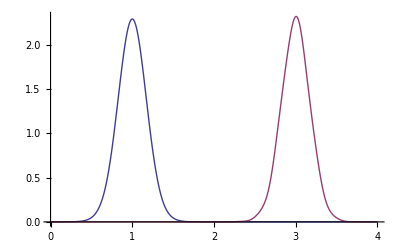

```mathematica
Plot[{1/(√(2 π) σX[[1]]) Exp[-(y - μX)^2/(2 σX[[1]]^2)] (1 + ∑_(m=3)^M α[[1,m-2]]/(m! σX[[1]]^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 σX[[1]])]),1/(√(2 π) σX[[2]]) Exp[-(y - 3 μX)^2/(2 σX[[2]]^2)] (1 + ∑_(m=3)^M α[[2,m-2]]/(m! σX[[2]]^m) 2^(-m/2) HermiteH[m,(y - 3 μX)/(√2 σX[[2]])])},{y,0,4},PlotRange->All]
```

```mathematica
optboundariesGCs[10,L,σΔ,SNRdB,M,μX]
```

1.94687

and how Gaussian is the actual distribution? ...

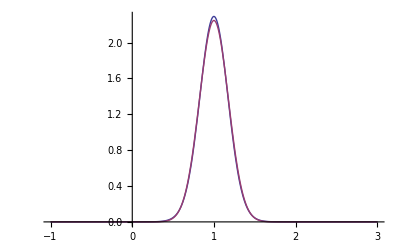

```mathematica
cdlGCparams=GC[L,σΔ,SNRdB,M,Δi];
cdlg0=cdlGCparams[[1]];
cdlσX=cdlGCparams[[2]];
cdlα=cdlGCparams[[3]];

Plot[{2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) cdlσX[[i]]) Exp[-(y - cdlg0[[i]])^2/(2 cdlσX[[i]]^2)] (1 + ∑_(m=2)^M cdlα[[i,m]]/((2 m)! cdlσX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - cdlg0[[i]])/(√2 cdlσX[[i]])]),1/(√(2 π) σX[[1]]) Exp[-(y - μX)^2/(2 σX[[1]]^2)]},{y,-1,3},PlotRange->All]
```

test over n and M ... (note: here, M≥2 required in order to evaluate σ_X) ...

```mathematica
allboundaries=ParallelTable[Quiet[optboundariesGCs[n,L,σΔ,SNRdB,m,μX]],{n,1,20},{m,2,M}];
allboundaries // MatrixForm
```

(2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2.
1.99049 | -1.06329 | 1.99046 | 31.8753 | 1.99043 | 4.45981 | 1.99039 | -27.8981 | 1.99035 | -27.8981 | 1.9903 | 17.2998 | 1.99025 | -0.946833 | 1.9902 | 4.46142 | 1.99015 | 31.8753 | 1.99011
1.99735 | 1.96711 | 1.98939 | 1.9831 | 1.9776 | 1.98103 | 1.97874 | 1.97998 | 1.98041 | 1.98013 | 1.98012 | 1.98025 | 1.98062 | 1.98162 | 1.98231 | 1.97999 | 1.97439 | 1.96542 | 1.95734
1.99836 | 2.00555 | 2.00146 | 1.99921 | 1.9987 | 1.99592 | 1.994 | 1.98975 | 1.98802 | 1.98996 | 1.99473 | 2.00676 | 2.00925 | 2.00349 | 1.99671 | 1.99142 | 1.99095 | 1.99466 | 1.99804
1.99831 | 1.99167 | 1.99533 | 1.97843 | 1.98678 | 1.96438 | 1.9753 | 1.95885 | 1.96024 | 1.9547 | 1.9496 | 1.95216 | 1.95174 | 1.95342 | 1.95453 | 1.95428 | 1.95393 | 1.95311 | 1.95202
1.99778 | 1.96854 | 1.99374 | 1.97732 | 1.98899 | 1.97581 | 1.98251 | 1.97436 | 1.97572 | 1.97224 | 1.97105 | 1.97082 | 1.97045 | 1.97895 | 1.98983 | 1.99381 | 1.98476 | 1.96465 | 1.94607
1.99778 | 1.97195 | 1.99365 | 1.98521 | 1.98794 | 1.9794 | 1.98073 | 1.96766 | 1.96789 | 1.956 | 1.94539 | 1.95078 | 2.06351 | 5.94237 | -2.53795 | 2.01396 | 1.98697 | 1.96244 | 1.94429
1.99799 | 1.98122 | 1.9936 | 1.98383 | 1.98601 | 1.96442 | 1.97671 | 1.95848 | 1.96169 | 1.95371 | 1.94655 | 1.94995 | 1.94729 | 1.95272 | 1.9586 | 1.95759 | 1.95574 | 1.94779 | 1.93628
1.99801 | 1.98092 | 1.99348 | 1.97863 | 1.98695 | 1.96973 | 1.97842 | 1.96702 | 1.96791 | 1.96282 | 1.95952 | 1.96147 | 1.96096 | 1.97385 | 1.98437 | 1.97946 | 1.9719 | 1.95843 | 1.94543
1.99795 | 1.97835 | 1.99355 | 1.98032 | 1.98746 | 1.9743 | 1.9792 | 1.96766 | 1.96796 | 1.96003 | 1.95372 | 1.9572 | 1.95308 | 1.9722 | 1.98919 | 1.98234 | 1.97376 | 1.9597 | 1.94687
1.99794 | 1.97836 | 1.99361 | 1.98182 | 1.9872 | 1.97247 | 1.97848 | 1.96394 | 1.96581 | 1.95778 | 1.95161 | 1.95461 | 1.95141 | 1.96196 | 1.9729 | 1.97066 | 1.96582 | 1.95314 | 1.93893
1.99796 | 1.97891 | 1.99359 | 1.98135 | 1.98706 | 1.97107 | 1.97848 | 1.96506 | 1.9666 | 1.9597 | 1.9547 | 1.95734 | 1.95506 | 1.96862 | 1.98104 | 1.97687 | 1.97031 | 1.95724 | 1.94433
1.99796 | 1.9789 | 1.99357 | 1.981 | 1.98715 | 1.97189 | 1.97867 | 1.96589 | 1.96693 | 1.95962 | 1.95404 | 1.95706 | 1.95406 | 1.96811 | 1.98087 | 1.97678 | 1.97018 | 1.95702 | 1.9438
1.99795 | 1.97881 | 1.99358 | 1.98113 | 1.98718 | 1.97211 | 1.97861 | 1.96535 | 1.96662 | 1.95912 | 1.95345 | 1.95638 | 1.95348 | 1.96621 | 1.97846 | 1.97494 | 1.96882 | 1.9557 | 1.94216
1.99795 | 1.97881 | 1.99358 | 1.98119 | 1.98715 | 1.9719 | 1.97859 | 1.96528 | 1.96663 | 1.95932 | 1.95384 | 1.9567 | 1.95395 | 1.96728 | 1.97977 | 1.97593 | 1.96962 | 1.95655 | 1.94334
1.99795 | 1.97883 | 1.99358 | 1.98116 | 1.98715 | 1.97189 | 1.9786 | 1.96542 | 1.96669 | 1.95936 | 1.95384 | 1.95675 | 1.9539 | 1.96726 | 1.97971 | 1.97591 | 1.96956 | 1.95644 | 1.94311
1.99795 | 1.97883 | 1.99358 | 1.98115 | 1.98716 | 1.97193 | 1.9786 | 1.9654 | 1.96667 | 1.95931 | 1.95376 | 1.95667 | 1.95382 | 1.96702 | 1.97944 | 1.97569 | 1.96939 | 1.95628 | 1.94294
1.99795 | 1.97882 | 1.99358 | 1.98116 | 1.98716 | 1.97192 | 1.9786 | 1.96538 | 1.96667 | 1.95932 | 1.95378 | 1.95668 | 1.95386 | 1.96712 | 1.97957 | 1.97579 | 1.96948 | 1.95638 | 1.94308
1.99795 | 1.97882 | 1.99358 | 1.98116 | 1.98716 | 1.97192 | 1.9786 | 1.96539 | 1.96667 | 1.95932 | 1.95379 | 1.95669 | 1.95386 | 1.96713 | 1.97957 | 1.97579 | 1.96948 | 1.95637 | 1.94304
1.99795 | 1.97882 | 1.99358 | 1.98116 | 1.98716 | 1.97192 | 1.9786 | 1.96539 | 1.96667 | 1.95932 | 1.95378 | 1.95669 | 1.95386 | 1.96711 | 1.97955 | 1.97577 | 1.96946 | 1.95636 | 1.94303)

```mathematica
100*Abs[(allboundaries[[-1,-1]]-allboundaries)/allboundaries[[-1,-1]]] // MatrixForm
```

(2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182 | 2.93182
2.44244 | 154.723 | 2.441 | 1540.49 | 2.43934 | 129.528 | 2.43731 | 1535.8 | 2.43503 | 1535.8 | 2.43261 | 790.352 | 2.43011 | 148.73 | 2.42759 | 129.611 | 2.42507 | 1540.49 | 2.42257
2.79539 | 1.23932 | 2.38584 | 2.06208 | 1.77908 | 1.95534 | 1.83775 | 1.90137 | 1.9234 | 1.90939 | 1.90875 | 1.91555 | 1.93467 | 1.98584 | 2.02146 | 1.90184 | 1.61388 | 1.15205 | 0.736377
2.84722 | 3.21754 | 3.00721 | 2.89128 | 2.86474 | 2.72184 | 2.62279 | 2.40446 | 2.31511 | 2.41512 | 2.66079 | 3.27952 | 3.40767 | 3.11168 | 2.76248 | 2.49002 | 2.46617 | 2.65703 | 2.83097
2.84491 | 2.50314 | 2.69163 | 1.82164 | 2.25149 | 1.09848 | 1.6608 | 0.81411 | 0.885516 | 0.600603 | 0.338073 | 0.469897 | 0.448129 | 0.534654 | 0.59143 | 0.578647 | 0.560702 | 0.518478 | 0.462573
2.81766 | 1.3128 | 2.60976 | 1.76455 | 2.36523 | 1.68692 | 2.03176 | 1.61222 | 1.68223 | 1.50328 | 1.4421 | 1.4299 | 1.41115 | 1.84852 | 2.40843 | 2.61345 | 2.14746 | 1.11253 | 0.156146
2.8176 | 1.48823 | 2.60511 | 2.17044 | 2.31138 | 1.8718 | 1.94028 | 1.26754 | 1.27943 | 0.667482 | 0.121446 | 0.398577 | 6.20055 | 205.829 | 230.618 | 3.6503 | 2.26138 | 0.998903 | 0.0645996
2.82857 | 1.96508 | 2.60249 | 2.0995 | 2.21169 | 1.10062 | 1.733 | 0.795093 | 0.960394 | 0.549288 | 0.180808 | 0.356006 | 0.218807 | 0.498726 | 0.801199 | 0.749032 | 0.653774 | 0.244999 | 0.347664
2.82922 | 1.94963 | 2.59635 | 1.83188 | 2.26043 | 1.3737 | 1.82112 | 1.23459 | 1.28005 | 1.01844 | 0.848449 | 0.949047 | 0.922786 | 1.58622 | 2.12717 | 1.8746 | 1.48554 | 0.792509 | 0.123278
2.82609 | 1.8176 | 2.59995 | 1.91911 | 2.28655 | 1.60899 | 1.86153 | 1.26745 | 1.28307 | 0.87464 | 0.550167 | 0.728884 | 0.51721 | 1.50117 | 2.3757 | 2.0228 | 1.58139 | 0.857629 | 0.197458
2.8259 | 1.81802 | 2.60287 | 1.9964 | 2.27317 | 1.51482 | 1.82443 | 1.07574 | 1.17223 | 0.758868 | 0.44123 | 0.595539 | 0.431098 | 0.97406 | 1.53713 | 1.42186 | 1.17294 | 0.519921 | 0.211373
2.82659 | 1.84662 | 2.6018 | 1.97214 | 2.26575 | 1.44314 | 1.8244 | 1.13384 | 1.21278 | 0.857895 | 0.600195 | 0.736054 | 0.618736 | 1.31699 | 1.95621 | 1.74132 | 1.40406 | 0.730903 | 0.0665163
2.82661 | 1.84606 | 2.60098 | 1.95403 | 2.27069 | 1.48489 | 1.83394 | 1.1764 | 1.22968 | 0.853485 | 0.566672 | 0.721796 | 0.567256 | 1.29071 | 1.94707 | 1.7366 | 1.39699 | 0.719777 | 0.039606
2.82649 | 1.84116 | 2.60129 | 1.96069 | 2.27185 | 1.49663 | 1.83108 | 1.14853 | 1.21367 | 0.828078 | 0.535958 | 0.686878 | 0.537487 | 1.193 | 1.8232 | 1.64218 | 1.32689 | 0.651632 | 0.0449998
2.82649 | 1.8415 | 2.60143 | 1.96355 | 2.27065 | 1.4858 | 1.82968 | 1.14486 | 1.21461 | 0.838135 | 0.556159 | 0.703217 | 0.561988 | 1.24773 | 1.89077 | 1.69294 | 1.36813 | 0.695383 | 0.015545
2.82651 | 1.84217 | 2.60137 | 1.96217 | 2.27059 | 1.48508 | 1.83069 | 1.15208 | 1.21769 | 0.840449 | 0.556172 | 0.706033 | 0.559352 | 1.24682 | 1.88782 | 1.69202 | 1.3652 | 0.689922 | 0.00391055
2.82651 | 1.84207 | 2.60135 | 1.96188 | 2.27081 | 1.4871 | 1.8307 | 1.15117 | 1.21667 | 0.837676 | 0.551957 | 0.701618 | 0.55532 | 1.23451 | 1.87387 | 1.68074 | 1.35668 | 0.681771 | 0.00492921
2.82651 | 1.842 | 2.60136 | 1.9621 | 2.27078 | 1.48691 | 1.83052 | 1.15006 | 1.21641 | 0.838084 | 0.55326 | 0.702374 | 0.557207 | 1.23977 | 1.88058 | 1.68575 | 1.36126 | 0.687041 | 0.00228481
2.82651 | 1.84202 | 2.60136 | 1.96211 | 2.27076 | 1.48664 | 1.83056 | 1.15044 | 1.21664 | 0.838435 | 0.553607 | 0.702956 | 0.557269 | 1.24008 | 1.88045 | 1.68591 | 1.36095 | 0.686237 | 0.000541923
2.82651 | 1.84202 | 2.60136 | 1.96208 | 2.27076 | 1.48671 | 1.83058 | 1.15053 | 1.21662 | 0.838275 | 0.553305 | 0.702676 | 0.556952 | 1.23903 | 1.87933 | 1.68497 | 1.36024 | 0.685606 | 0.)

previous result for averaged conditional Gram-Charlier pdfs ...

```mathematica
cdlboundary=optboundaries[20,L,σΔ,SNRdB,M]
```

1.96229

```mathematica
100*Abs[(cdlboundary-allboundaries)/cdlboundary] // MatrixForm
```

(1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174 | 1.92174
1.43716 | 154.186 | 1.43573 | 1524.39 | 1.43409 | 127.276 | 1.43208 | 1521.71 | 1.42982 | 1521.71 | 1.42743 | 781.615 | 1.42495 | 148.251 | 1.42245 | 127.358 | 1.41996 | 1524.39 | 1.41749
1.78665 | 0.245846 | 1.38112 | 1.06054 | 0.780317 | 0.954847 | 0.83841 | 0.9014 | 0.923219 | 0.909344 | 0.908713 | 0.915445 | 0.934374 | 0.985045 | 1.02032 | 0.901872 | 0.616736 | 0.159434 | 0.252158
1.83797 | 2.20465 | 1.99639 | 1.8816 | 1.85532 | 1.71382 | 1.61574 | 1.39956 | 1.31108 | 1.41011 | 1.65337 | 2.26602 | 2.39292 | 2.09983 | 1.75406 | 1.48428 | 1.46066 | 1.64964 | 1.82188
1.83568 | 1.49726 | 1.68391 | 0.822453 | 1.24809 | 0.106395 | 0.663192 | 0.175188 | 0.104483 | 0.3866 | 0.646554 | 0.516023 | 0.537577 | 0.451902 | 0.395683 | 0.40834 | 0.426109 | 0.467919 | 0.523276
1.8087 | 0.318607 | 1.60284 | 0.76592 | 1.36071 | 0.689059 | 1.03051 | 0.615088 | 0.684417 | 0.507223 | 0.44664 | 0.434561 | 0.415996 | 0.849075 | 1.40348 | 1.60649 | 1.14508 | 0.120301 | 0.826696
1.80864 | 0.492321 | 1.59823 | 1.16783 | 1.30739 | 0.872122 | 0.93993 | 0.27379 | 0.28557 | 0.320377 | 0.861055 | 0.586644 | 5.15839 | 202.828 | 229.336 | 2.63317 | 1.25788 | 0.00779121 | 0.917343
1.8195 | 0.964484 | 1.59564 | 1.09758 | 1.20868 | 0.108506 | 0.734685 | 0.194019 | 0.0303393 | 0.437411 | 0.802276 | 0.628797 | 0.764649 | 0.487477 | 0.187972 | 0.239628 | 0.333951 | 0.738714 | 1.32556
1.82014 | 0.949193 | 1.58956 | 0.832593 | 1.25694 | 0.378906 | 0.821941 | 0.241168 | 0.286175 | 0.0271343 | 0.141186 | 0.041575 | 0.0675789 | 0.589347 | 1.12499 | 0.874899 | 0.489655 | 0.196577 | 0.859241
1.81705 | 0.818459 | 1.59312 | 0.918965 | 1.2828 | 0.611895 | 0.861955 | 0.273704 | 0.289171 | 0.115252 | 0.436541 | 0.259578 | 0.469175 | 0.505126 | 1.37108 | 1.02164 | 0.584564 | 0.132096 | 0.785789
1.81686 | 0.81887 | 1.59602 | 0.995502 | 1.26956 | 0.518644 | 0.825215 | 0.0838764 | 0.179421 | 0.229888 | 0.544409 | 0.391614 | 0.554441 | 0.0168074 | 0.540733 | 0.426602 | 0.180119 | 0.46649 | 1.19061
1.81754 | 0.847192 | 1.59496 | 0.971482 | 1.26221 | 0.447671 | 0.825183 | 0.1414 | 0.219568 | 0.131833 | 0.387004 | 0.252478 | 0.368645 | 0.322753 | 0.955701 | 0.742922 | 0.40897 | 0.257578 | 0.915446
1.81757 | 0.846637 | 1.59415 | 0.953544 | 1.2671 | 0.48901 | 0.834637 | 0.183546 | 0.236305 | 0.136199 | 0.420198 | 0.266596 | 0.41962 | 0.296739 | 0.946653 | 0.738251 | 0.401974 | 0.268596 | 0.942092
1.81744 | 0.841785 | 1.59445 | 0.960142 | 1.26825 | 0.500637 | 0.831806 | 0.15595 | 0.220454 | 0.161357 | 0.45061 | 0.301172 | 0.449097 | 0.199987 | 0.824004 | 0.644759 | 0.332563 | 0.336072 | 1.02587
1.81745 | 0.842118 | 1.5946 | 0.962974 | 1.26706 | 0.489909 | 0.830418 | 0.15232 | 0.221384 | 0.151398 | 0.430607 | 0.284993 | 0.424836 | 0.254174 | 0.890903 | 0.695022 | 0.373394 | 0.29275 | 0.965917
1.81747 | 0.842781 | 1.59453 | 0.961604 | 1.267 | 0.489195 | 0.831418 | 0.159465 | 0.224436 | 0.149108 | 0.430595 | 0.282204 | 0.427446 | 0.253275 | 0.887986 | 0.694112 | 0.37049 | 0.298157 | 0.977437
1.81746 | 0.842687 | 1.59451 | 0.961314 | 1.26721 | 0.491195 | 0.831431 | 0.15856 | 0.223426 | 0.151853 | 0.434768 | 0.286576 | 0.431439 | 0.24109 | 0.874175 | 0.682941 | 0.36206 | 0.306228 | 0.98619
1.81746 | 0.842617 | 1.59453 | 0.961535 | 1.26719 | 0.491006 | 0.831248 | 0.157464 | 0.223167 | 0.15145 | 0.433478 | 0.285827 | 0.42957 | 0.246299 | 0.880817 | 0.6879 | 0.366593 | 0.30101 | 0.979047
1.81746 | 0.842634 | 1.59453 | 0.961546 | 1.26716 | 0.490747 | 0.831288 | 0.157845 | 0.22339 | 0.151101 | 0.433135 | 0.285252 | 0.429509 | 0.246605 | 0.880692 | 0.688059 | 0.366285 | 0.301806 | 0.980772
1.81746 | 0.842639 | 1.59452 | 0.961519 | 1.26717 | 0.490812 | 0.831307 | 0.157929 | 0.223372 | 0.151261 | 0.433434 | 0.285529 | 0.429822 | 0.245567 | 0.879582 | 0.687121 | 0.365585 | 0.302431 | 0.981309)

#### σ_Δ^2 = 0.005, 20 dB

```mathematica
σΔ=√0.005;
SNRdB=20;
```

```mathematica
DistributeDefinitions[σΔ,SNRdB];
```

```mathematica
gq=GaussianQuadratureWeights[10,0,1/2];
Δi=gq[[All,1]];
wi=gq[[All,2]];
μX=Total[2*wi*g[Δi,0]*Exp[Cos[2 π Δi]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2]];
GCparams=Table[singleGC[L,σΔ,SNRdB,M,Δi,wi,ω0,μX],{ω0,1,3,2}];
σX=GCparams[[All,1]];
α=GCparams[[All,2]];
```

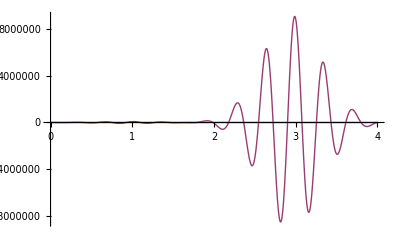

```mathematica
Plot[{1/(√(2 π) σX[[1]]) Exp[-(y - μX)^2/(2 σX[[1]]^2)] (1 + ∑_(m=3)^M α[[1,m-2]]/(m! σX[[1]]^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 σX[[1]])]),1/(√(2 π) σX[[2]]) Exp[-(y - 3 μX)^2/(2 σX[[2]]^2)] (1 + ∑_(m=3)^M α[[2,m-2]]/(m! σX[[2]]^m) 2^(-m/2) HermiteH[m,(y - 3 μX)/(√2 σX[[2]])])},{y,0,4},PlotRange->All]
```

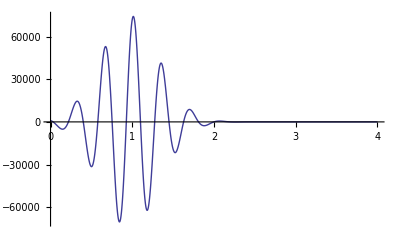

```mathematica
Plot[1/(√(2 π) σX[[1]]) Exp[-(y - μX)^2/(2 σX[[1]]^2)] (1 + ∑_(m=3)^M α[[1,m-2]]/(m! σX[[1]]^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 σX[[1]])]),{y,0,4},PlotRange->All]
```

first check if this is a precision issue ...

```mathematica
$MaxExtraPrecision=100;

ω0=1;

σΔ=SetPrecision[σΔ,100];
Δi=SetPrecision[Δi,100];
wi=SetPrecision[wi,100];
μX=SetPrecision[μX,100];
σv=SetPrecision[√((L^2-1)/(3*Log[2,L]*10^(SNRdB/10))),100];
μ=Table[0,{M+1}];
For[n=1,n≤Length[Δi],
g0=SetPrecision[g[Δi[[n]],0],100];
gk=SetPrecision[Join[Table[g[Δi[[n]],k],{k,-40,-1}],Table[g[Δi[[n]],k],{k,1,40}]],100];
κ=SetPrecision[Table[(-1)^(m+1) Tm[[m]] (L^(2 m) - 1)/(2^(2 m) - 1) Total[gk^(2 m)],{m,1,Ceiling[M/2]}],100];
κ[[1]]+=SetPrecision[σv^2,100];
κ=Riffle[κ,0];
PrependTo[κ,SetPrecision[ω0 (g0-μX),100]];
μXΔ={1,SetPrecision[ω0 (g0-μX),100]};
For[m=2,m≤M,
AppendTo[μXΔ,SetPrecision[∑_(i=0)^(m-1) Binomial[m - 1,i] κ[[m-i]] μXΔ[[i+1]],100]];
m++];
μ+=SetPrecision[2*wi[[n]]*μXΔ*Exp[Cos[2 π Δi[[n]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2],100];
n++];
σX=SetPrecision[√μ[[3]],100];
α=Table[SetPrecision[m! ∑_(i=0)^Floor[m/2] (-1)^i (σX^(2 i) μ[[m - 2 i + 1]])/(2^i i! (m - 2 i)!),100],{m,3,M}];
```

```mathematica
Clear[m];
Plot[1/(√(2 π) σX) Exp[-(y - μX)^2/(2 σX^2)] (1 + ∑_(m=3)^M α[[m-2]]/(m! σX^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 σX)]),{y,0,4},PlotRange->All]
```

-Graphics-

doesn’t seem to be a precision issue ... compare moments to those evaluated numerically from averaged conditional Gram-Charlier pdfs ...

```mathematica
cdlGCparams=GC[L,σΔ,SNRdB,M,Δi];
cdlg0=cdlGCparams[[1]];
cdlσX=cdlGCparams[[2]];
cdlα=cdlGCparams[[3]];
```

```mathematica
SetPrecision[μ,6]
checkμ=ParallelTable[Quiet[2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) cdlσX[[i]]) NIntegrate[(y - μX)^n Exp[-(y - cdlg0[[i]])^2/(2 cdlσX[[i]]^2)] (1 + ∑_(m=2)^M cdlα[[i,m]]/((2 m)! cdlσX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - cdlg0[[i]])/(√2 cdlσX[[i]])]),{y,-∞,∞}]],{n,2,M}]
```

{1.,-1.18202×10^-6,0.0628842,-0.00292915,0.0192388,-0.00433526,0.0158899,-0.0100209,0.0289226,-0.0360276,0.0962811,-0.1763,0.467695,-1.04306,2.80587,-6.94483,19.0284,-50.0516,139.652,-382.125,1084.28}

{0.0628842,-0.00292915,0.0192388,-0.00433526,0.0158899,-0.0100209,0.0289226,-0.0360276,0.0962811,-0.1763,0.467695,-1.04306,2.80584,-6.94473,19.027,-50.045,139.573,-381.688,1080.17}

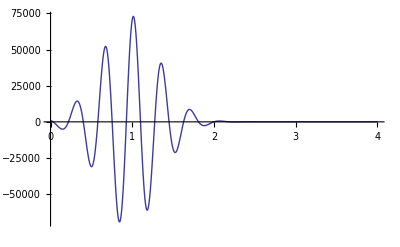

```mathematica
checkμ=Join[{1,0},checkμ];
checkσX=√checkμ[[3]];
checkα=Table[m! ∑_(i=0)^Floor[m/2] (-1)^i (checkσX^(2 i) checkμ[[m - 2 i + 1]])/(2^i i! (m - 2 i)!),{m,3,M}];
Clear[m];
Plot[1/(√(2 π) checkσX) Exp[-(y - μX)^2/(2 checkσX^2)] (1 + ∑_(m=3)^M checkα[[m-2]]/(m! checkσX^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 checkσX)]),{y,0,4},PlotRange->All]
```

```mathematica
checkμ=SetPrecision[checkμ,100];
checkσX=SetPrecision[√checkμ[[3]],100];
checkα=Table[SetPrecision[m! ∑_(i=0)^Floor[m/2] (-1)^i (checkσX^(2 i) checkμ[[m - 2 i + 1]])/(2^i i! (m - 2 i)!),100],{m,3,M}];
Clear[m];
Plot[1/(√(2 π) checkσX) Exp[-(y - μX)^2/(2 checkσX^2)] (1 + ∑_(m=3)^M checkα[[m-2]]/(m! checkσX^m) 2^(-m/2) HermiteH[m,(y - μX)/(√2 checkσX)]),{y,0,4},PlotRange->All]
```

-Graphics-

and how Gaussian is the actual distribution? ...

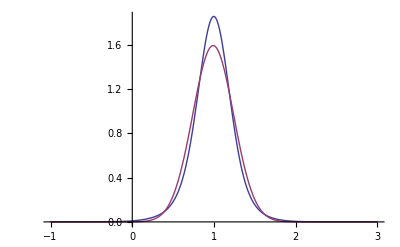

```mathematica
Plot[{2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) cdlσX[[i]]) Exp[-(y - cdlg0[[i]])^2/(2 cdlσX[[i]]^2)] (1 + ∑_(m=2)^M cdlα[[i,m]]/((2 m)! cdlσX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - cdlg0[[i]])/(√2 cdlσX[[i]])]),1/(√(2 π) σX) Exp[-(y - μX)^2/(2 σX^2)]},{y,-1,3},PlotRange->All]
```

suspect that large Δ moments are dominating ... possibly alleviated by windowing Δ to [-0.25, 0.25] but not overly in favour of this approach ...

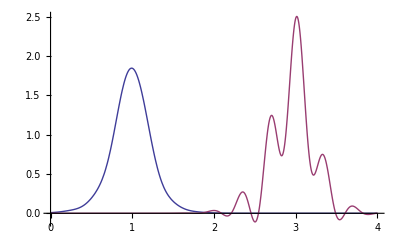

```mathematica
gqwin=GaussianQuadratureWeights[10,0,1/4];
Δiwin=gqwin[[All,1]];
wiwin=gqwin[[All,2]];
μXwin=Total[2*wiwin*g[Δiwin,0]*Exp[Cos[2 π Δiwin]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2]];
GCwinparams=Table[singleGC[L,σΔ,SNRdB,M,Δiwin,wiwin,ω0,μXwin],{ω0,1,3,2}];
σXwin=GCwinparams[[All,1]];
αwin=GCwinparams[[All,2]];
Plot[{1/(√(2 π) σXwin[[1]]) Exp[-(y - μXwin)^2/(2 σXwin[[1]]^2)] (1 + ∑_(m=3)^M αwin[[1,m-2]]/(m! σXwin[[1]]^m) 2^(-m/2) HermiteH[m,(y - μXwin)/(√2 σXwin[[1]])]),1/(√(2 π) σXwin[[2]]) Exp[-(y - 3 μXwin)^2/(2 σXwin[[2]]^2)] (1 + ∑_(m=3)^M αwin[[2,m-2]]/(m! σXwin[[2]]^m) 2^(-m/2) HermiteH[m,(y - 3 μXwin)/(√2 σXwin[[2]])])},{y,0,4},PlotRange->All]
```

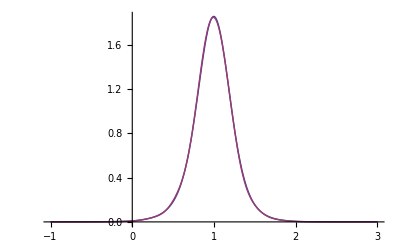

```mathematica
Plot[{2 ∑_(i=1)^Length[Δi] wi[[i]] Exp[Cos[2 π Δi[[i]]]/(2 π σΔ)^2]/BesselI[0,1/(2 π σΔ)^2] 1/(√(2 π) cdlσX[[i]]) Exp[-(y - cdlg0[[i]])^2/(2 cdlσX[[i]]^2)] (1 + ∑_(m=2)^M cdlα[[i,m]]/((2 m)! cdlσX[[i]]^(2 m)) 2^-m HermiteH[2 m,(y - cdlg0[[i]])/(√2 cdlσX[[i]])]),1/(√(2 π) σXwin[[1]]) Exp[-(y - μXwin)^2/(2 σXwin[[1]]^2)] (1 + ∑_(m=3)^M αwin[[1,m-2]]/(m! σXwin[[1]]^m) 2^(-m/2) HermiteH[m,(y - μXwin)/(√2 σXwin[[1]])])},{y,-1,3},PlotRange->All]
```

... windowing sufficient for ω_0=1 but not ω_0=3